# Code for case study #1, a deterministic, continuous-time model, inspired by Armstrong and McGehee.

Table 1 in the main text corresponds to b1=1. Table 2 in the main text corresponds to b1 = 100. Change the parameter value below (in the first section) to switch between the two versions of the model.

```mathematica
(* ctrl+a to select all, then shift+enter to run the whole notebook *)
SeedRandom[20]
```

## Write Equations, select parameters, and simulate to make sure that species can coexist

```mathematica
(*equations for pop dynamic: consumers N1, N2, and N3; resources R1 and R2; consumption rates cjk; half saturation constant η for consumer 2 functional responses; consumer death rate is d; maximum growth rate of resources is r1 and r2; carrying capacity for resources is k*)
dN1dt:=b1 N1[t](( c11 R1[t]+c21 R2[t])-d);
dN2dt:=b2 N2[t](c12 R1[t]+((c22 R2[t])/(η+ R2[t]))-d);
dN3dt:=b3 N3[t](( c13 R1[t] +c23 R2[t])-d);
dR1dt:= R1[t](r1(1-R1[t]/k1)-c11 N1[t] -c12 N2[t] -c13 N3[t]);
dR2dt:= R2[t](r2(1-R2[t]/k2)-c21 N1[t] -(c22 N2[t])/(η+ R2[t]) -c23  N3[t]);
```

```mathematica
(* simplify the more general equations above by making species symmetric, in that they either respond strongly, c , or weakly, ϵ, to the resources. The exceptions are that Species 1 heavily consumes resources 1 at rate c; species 2 and 3 consume at about the same rate (but see nonlinear response for species 3). All other resource consumption is small at rate ϵ
Species 1 specializes on resource 1
Species 2 specializes on resource 2
Species 3 specializes on resource 3 *)
r1 = r2 = r;
k1 = k2 = k;
c11=c;
c22=c;
c23=c;
c21=ϵ;
c12=ϵ;
c13=ϵ;
```

```mathematica
(* give values to model parameters *)
c=1;
ϵ=0.05;
η=0.4;
r=1;
k=1.5;
d=0.47;
b1=100; (* or b = 1 (for table 1) or b = 100 (for table 3) *)
b2=1;b3=1;
```

### Make sure that all species can coexist together

```mathematica
(*simulation parameters*)
tMax=2000;
burnIn = 1000;
plotTMax =500;
N1Init=0.1;
N2Init=0.1;
N3Init =0.1;
R1Init =0.1;
R2Init=0.1;
(* numerically solve differential equations *)
sol=NDSolve[{N1'[t]==dN1dt,N2'[t]==dN2dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N2[0]==N2Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init},{N1,N2,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
```

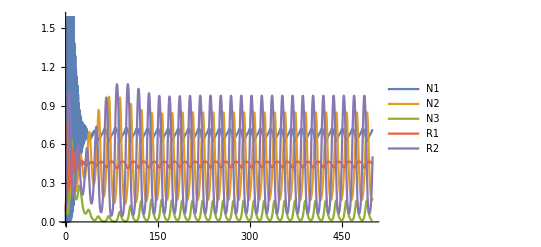

```mathematica
(* all species can coexist together *)
Plot[Evaluate[{N1[t],N2[t],N3[t],R1[t], R2[t]}/.sol],{t,0,plotTMax},PlotLegends->{"N1","N2","N3","R1","R2"}]
```

```mathematica
(* average densities of species*)
NBarAll=Integrate[Evaluate[{N1[t],N2[t], N3[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
(* average densities of resources*)
RBarAll=Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.676475,0.436651,0.0656864}

{0.447581,0.448374}

### Make sure that all pairs of species can coexist. This means that the mutual invasibility criterion is applicable.

#### Consumers 1 and 2

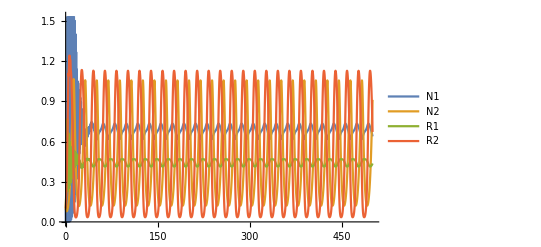

```mathematica
(* consumer 1 and 2 can coexist *)
sol=NDSolve[{N1'[t]==dN1dt,N2'[t]==dN2dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N2[0]==N2Init,R1[0]==R1Init,R2[0]==R2Init}/.N3[t]->0,{N1,N2,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
Plot[Evaluate[{N1[t],N2[t],R1[t], R2[t]}/.sol],{t,0,plotTMax},PlotLegends->{"N1","N2","R1","R2"}]
```

```mathematica
(* average densities of species*)
Integrate[Evaluate[{N1[t],N2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
(* average densities of resources*)
Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.680841,0.455236}

{0.44466,0.506785}

#### Consumers 1 and 3

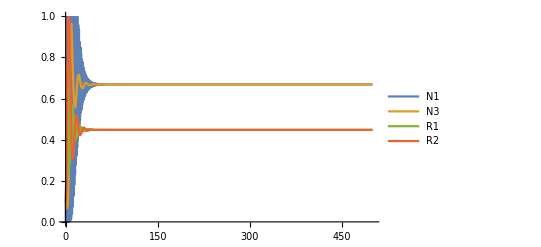

```mathematica
(* consumer 1 and 3 can coexist *)
sol=NDSolve[{N1'[t]==dN1dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init}/.N2[t]->0,{N1,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
Plot[Evaluate[{N1[t],N3[t],R1[t], R2[t]}/.sol],{t,0,plotTMax},PlotLegends->{"N1","N3","R1","R2"}]
```

```mathematica
(* average densities of species*)
Integrate[Evaluate[{N1[t], N3[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
(* average densities of resources*)
Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.668178,0.668178}

{0.447619,0.447619}

#### Consumers 2 and 3

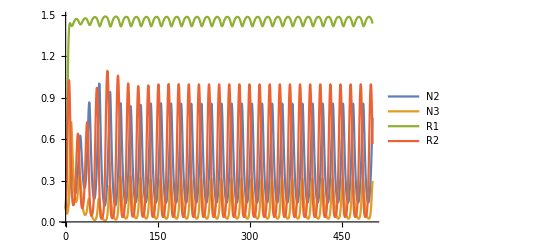

```mathematica
(* consumer 2 and 3 can coexist *)
sol=NDSolve[{N2'[t]==dN2dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N2[0]==N2Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init}/.N1[t]->0,{N2,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
Plot[Evaluate[{N2[t],N3[t],R1[t], R2[t]}/.sol],{t,0,plotTMax},PlotLegends->{"N2","N3","R1","R2"}]
```

```mathematica
(* average densities of species*)
Integrate[Evaluate[{N2[t], N3[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
(* average densities of resources*)
Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.406885,0.1206}

{1.46047,0.398425}

## Get sensitivities to competition and nonlinear responses to competition: Fix R1 at the temporal mean and solve for R2.

```mathematica
(* RStar contains the equilibrium limiting factors, 3 rows (one per species) X 2 column (one per factor) *)
RStar=ConstantArray[0,{3,2}];
```

```mathematica
(* set the equilibrium level of R1 to the temporal mean of R1 in the community where all species are present *)
RStar[[1,1]]=RStar[[2,1]]=RStar[[3,1]] = RBarAll[[1]];
```

```mathematica
(* now that R1 is fixed, solve for R2 *)
RStar[[1,2]]=R2[t]/.Solve[(dN1dt/N1[t]/.{R1[t]->RStar[[1,1]]} )==0,R2[t]][[1]];
RStar[[2,2]]=R2[t]/.Solve[(dN2dt/N2[t]/.{R1[t]->RStar[[2,1]]} )==0,R2[t]][[1]];
RStar[[3,2]]=R2[t]/.Solve[(dN3dt/N3[t]/.{R1[t]->RStar[[3,1]]} )==0,R2[t]][[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*  double check and make sure RStar produces zero growth rates *)
dN1dt/N1[t]/.{R1[t]->RStar[[1,1]],R2[t]->RStar[[1,2]]}
dN2dt/N2[t]/.{R1[t]->RStar[[2,1]],R2[t]->RStar[[2,2]]}
dN3dt/N3[t]/.{R1[t]->RStar[[3,1]],R2[t]->RStar[[3,2]]}
```

0.

-5.55112×10^-17

0.

```mathematica
(* Phi contains the sensitivities to regulating ractors, 3 rows (one per species) X 2 column (one per factor) *)
prePhi=D[{dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]},{{R1[t],R2[t]}}];
```

```mathematica
(* make species x resource matrix of senstivities to resources, evaluated at the user-specified equiblirium values of the resources *)
Phi=Table[prePhi[[i]]/.{R1[t]->RStar[[i,1]],R2[t]->RStar[[i,2]]},{i,1,3}]//FullSimplify;
```

```mathematica
Phi//MatrixForm
```

(100 | 5.
0.05 | 0.762807
0.05 | 1)

```mathematica
(*make species x resource x resource array of nonlinear responses to regulating factors *)
prePsi=D[{dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]},{{R1[t],R2[t]}},{{R1[t],R2[t]}}];
```

```mathematica
(*...evaluate at the user-specified equiblirium values of the resources *) 
Psi=Table[prePsi[[i]]/.{R1[t]->RStar[[i,1]],R2[t]->RStar[[i,2]]},{i,1,3}];
```

```mathematica
Psi//MatrixForm
```

((0
0) | (0
0)
(0
0) | (0
-2.10679)
(0
0) | (0
0))

## Functions for computing coexistence mechanisms

#### small-noise

```mathematica
(* regular small-noise coexistence mechanisms - used with the scaling factors *)
rPrime[q_, Phi_, RStar_]:=q.Total[(Phi*(-RStar)),{2}]

rPrimeF1[q_, Phi_, RStar_]:=q.Total[(Phi[[;;,1]]*(-RStar[[;;,1]]))]
rPrimeF2[q_, Phi_, RStar_]:=q.Total[(Phi[[;;,2]]*(-RStar[[;;,2]]))]

deltaRho[q_, Phi_, RBar_]:=q.Phi.RBar

deltaRhoF1[q_, Phi_, RBar_]:= q.Phi[[;;,1]]*RBar[[1]]
deltaRhoF2[q_, Phi_, RBar_]:= q.Phi[[;;,2]]*RBar[[2]]

deltaN[q_, Psi_, RVar_]:=(1/2)q.(Psi[[1;;3,2,2]]*RVar[[2]])

(* new small-noise coexistence mechanisms - RStar is not shunted to rPrime - used with the simple comparison, generation time scaling, and beta scaling *)
deltaRhoNew[q_, Phi_, RBar_, RStar_]:=q.Phi.RBar + q.Total[(Phi*(-RStar)),{2}]

deltaRhoF1New[q_, Phi_, RBar_, RStar_]:=q.Phi[[;;,1]]*RBar[[1]] + q.(Phi[[;;,1]]*(-RStar[[;;,1]]))
deltaRhoF2New[q_, Phi_, RBar_, RStar_]:=q.Phi[[;;,2]]*RBar[[2]] + q.(Phi[[;;,2]]*(-RStar[[;;,2]]))

deltaNNew[q_, Psi_, RVar_]:=(1/2)q.(Psi[[1;;3,2,2]]*RVar[[2]])
```

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
rPrimeE[q_,  avgGRF1F2Fixed_]:=q.avgGRF1F2Fixed
deltaNE[q_,avgGRF1F2Fixed_,avgGR_]:=q.(avgGR-avgGRF1F2Fixed)

(* new exact coexistence mechansism -  RStar is not shunted to rPrime - used with the simple comparison, generation time scaling, and beta scaling *)
deltaRhoENew[q_, avgGRF1F2Fixed_]:=q.avgGRF1F2Fixed
deltaRhoF2ENew[q_, avgGRF1Fixed_]:=q.avgGRF1Fixed
deltaRhoF1ENew[q_, avgGRF2Fixed_]:=q.avgGRF2Fixed
deltaRhoF1XF2ENew[q_, avgGRF1Fixed_,  avgGRF2Fixed_,  avgGRF1F2Fixed_]:=q.(avgGRF1F2Fixed-avgGRF1Fixed-avgGRF2Fixed)

deltaNENew[q_, avgGRF1F2Fixed_,avgGR_]:=q.(avgGR-avgGRF1F2Fixed)
```

### Invader-invader comparisons

#### small-noise

```mathematica
(* new small-noise coexistence mechanisms - RStar is not shunted to rPrime - used with the simple comparison, generation time scaling, and beta scaling *)
deltaRhoNewII[Phi_, RBarLow_, RBarHigh_, spInd_]:=Phi[[spInd,;;]].(RBarLow-RBarHigh)

deltaRhoF1NewII[ Phi_, RBarLow_, RBarHigh_, spInd_]:=Phi[[spInd,1]]*(RBarLow[[1]]-RBarHigh[[1]])
deltaRhoF2NewII[ Phi_, RBarLow_, RBarHigh_, spInd_]:= Phi[[spInd,2]]*(RBarLow[[2]]-RBarHigh[[2]])

deltaNNewII[Psi_, RVarLow_, RVarHigh_, spInd_]:=(1/2)*Psi[[spInd,2,2]]*(RVarLow[[2]]-RVarHigh[[2]])
```

#### exact

```mathematica
(* regular exact coexistence mechansism - used with scaling factors *)
rPrimeEII[avgGRF1F2FixedLow_,avgGRF1F2FixedHigh_, spInd_]:=avgGRF1F2FixedLow[[spInd]] - avgGRF1F2FixedHigh[[spInd]]
deltaNEII[avgGRF1F2FixedLow_,avgGRLow_,avgGRF1F2FixedHigh_, avgGRHigh_, spInd_]:=(avgGRLow[[spInd]]-avgGRF1F2FixedLow[[spInd]])-(avgGRHigh[[spInd]]-avgGRF1F2FixedHigh[[spInd]])

(* new exact coexistence mechansism -  RStar is not shunted to rPrime - used with the simple comparison, generation time scaling, and beta scaling *)
deltaRhoENewII[avgGRF1F2FixedLow_,avgGRF1F2FixedHigh_, spInd_]:=avgGRF1F2FixedLow[[spInd]] - avgGRF1F2FixedHigh[[spInd]]
deltaRhoF2ENewII[avgGRF1FixedLow_,avgGRF1FixedHigh_, spInd_]:=avgGRF1FixedLow[[spInd]] - avgGRF1FixedHigh[[spInd]]
deltaRhoF1ENewII[avgGRF2FixedLow_, avgGRF2FixedHigh_, spInd_]:=avgGRF2FixedLow[[spInd]] - avgGRF2FixedHigh[[spInd]]
deltaRhoF1XF2ENewII[avgGRF1FixedLow_,  avgGRF2FixedLow_,  avgGRF1F2FixedLow_, avgGRF1FixedHigh_,  avgGRF2FixedHigh_,  avgGRF1F2FixedHigh_, spInd_]:=(avgGRF1F2FixedLow[[spInd]]-avgGRF1FixedLow[[spInd]]-avgGRF2FixedLow[[spInd]])- (avgGRF1F2FixedHigh[[spInd]]-avgGRF1FixedHigh[[spInd]]-avgGRF2FixedHigh[[spInd]])

deltaNENewII[ avgGRF1F2FixedLow_,avgGRLow_, avgGRF1F2FixedHigh_,avgGRHigh_, spInd_]:=(avgGRLow[[spInd]]-avgGRF1F2FixedLow[[spInd]])-(avgGRHigh[[spInd]]-avgGRF1F2FixedHigh[[spInd]])
```

## get intermediate quantities for invader-invader comparison, quantities corresponding to a community with all species at typical densities

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0.3;
N3Init =0.3;
R1Init =0.3;
R2Init=0.3;
burnIn=1000;
tMax=2000;
plotTMax = 500;
```

```mathematica
(* simulate to get data for coexistence mechanism calculations*)
sol=NDSolve[{N1'[t]==dN1dt,N2'[t]==dN2dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N2[0]==N2Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init},{N1,N2,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
```

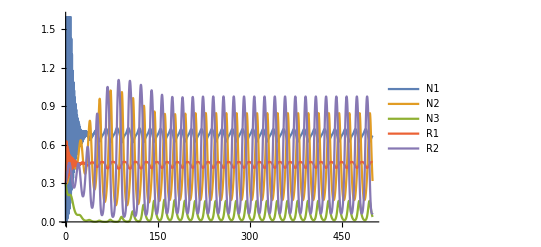

```mathematica
(* plot to make sure everything works as expected - the residents can coexist, no numerical problems, etc. *)
Plot[Evaluate[{N1[t],N2[t],N3[t],R1[t], R2[t]}/.sol],{t,0, plotTMax},PlotLegends->{"N1","N2","N3","R1","R2"}]
```

```mathematica
(* get the temporal mean of resource levels *)
RBarHigh= Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.447576,0.44846}

```mathematica
(* the mean of the square of resource levels, intermediate quantity in the calculation of resource variation *)
RSqBarHigh=Integrate[Evaluate[{R1Sq[t],R2Sq[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.200608,0.312386}

```mathematica
(* temporal variation in resource levels *)
RVarHigh=RSqBarHigh-RBarHigh^2
```

{0.000283627,0.11127}

```mathematica
(* intermediate quantities needed for the computation of exact coexistence mechanisms *)
(* functions to give per-capita growth rates of the consumers *)
r1Func=Interpolation[Table[{t,dN1dt/N1[t]/.sol},{t,burnIn,tMax,0.1}]];
r2Func=Interpolation[Table[{t,dN2dt/N2[t]/.sol},{t,burnIn,tMax,0.1}]];
r3Func=Interpolation[Table[{t,dN3dt/N3[t]/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
r1F1FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R1[t]->RStar[[1,1]])/.sol},{t,burnIn,tMax,0.1}]];
r2F1FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R1[t]->RStar[[2,1]])/.sol},{t,burnIn,tMax,0.1}]];
r3F1FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R1[t]->RStar[[3,1]])/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
r1F2FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R2[t]->RStar[[1,2]])/.sol},{t,burnIn,tMax,0.1}]];
r2F2FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R2[t]->RStar[[2,2]])/.sol},{t,burnIn,tMax,0.1}]];
r3F2FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R2[t]->RStar[[3,2]])/.sol},{t,burnIn,tMax,0.1}]];

(* long-term average growth rates of the consumers *)
avgGRHigh=Integrate[{r1Func[t],r2Func[t],r3Func[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
avgGRF1FixedHigh=Integrate[{r1F1FixedFunc[t],r2F1FixedFunc[t],r3F1FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
avgGRF2FixedHigh=Integrate[{r1F2FixedFunc[t],r2F2FixedFunc[t],r3F2FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where both resources are fixed; no simulation data needed*)
avgGRF1F2FixedHigh={dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]}/.{R1[t]->RBarHigh[[1]], R2[t]->RBarHigh[[2]]}
```

{-0.0000502173,0.00056747,0.000838857}

{0.000393112,0.000567692,0.000839078}

{-0.000443329,-2.21665×10^-7,-2.21665×10^-7}

{-0.0000502174,0.0809365,0.000838857}

## Invasion analysis: species 1 is the invader

```mathematica
(* simulation parameters *)
N1Init=0;
N2Init=0.3;
N3Init =0.3;
R1Init =0.3;
R2Init=0.3;
burnIn=1000;
tMax=2000;
plotTMax = 500;
```

```mathematica
(* simulate to get data for coexistence mechanism calculations*)
sol=NDSolve[{N2'[t]==dN2dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N2[0]==N2Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init}/.N1[t]->0,{N2,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
```

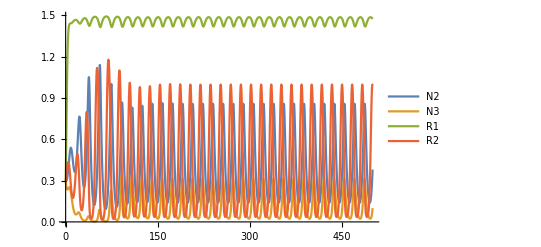

```mathematica
(* plot to make sure everything works as expected - the residents can coexist, no numerical problems, etc. *)
Plot[Evaluate[{N2[t],N3[t],R1[t], R2[t]}/.sol],{t,0, plotTMax},PlotLegends->{"N2","N3","R1","R2"}]
```

```mathematica
(* get the temporal mean of resource levels *)
RBar1 = Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{1.46046,0.396711}

```mathematica
(* examine mean resource fluctuations (away from the equilbirium levels *)
ConstantArray[RBar1,3]-RStar//MatrixForm
```

(1.01288 | -0.0516705
1.01288 | 0.0725705
1.01288 | -0.05091)

```mathematica
(* the mean of the square of resource levels, intermediate quantity in the calculation of resource variation *)
RSqBar1=Integrate[Evaluate[{R1Sq[t],R2Sq[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{2.13348,0.279891}

```mathematica
(* temporal variation in resource levels *)
RVar1=RSqBar1-RBar1^2
```

{0.000548681,0.122511}

```mathematica
(* scaling factors *)
preQ = Phi[[1]].Inverse[Drop[Phi,{1}]];
q1 = Insert[-preQ,1,1]//N
(* The simple comparison *)
noQ1 = {1,-1/2,-1/2}//N
(* generation time scaling and beta scaling (the methods are equivalent in this model) *)
GTS1 = {1,-(1/2)(b1/b2),-(1/2)(b1/b3)}//N
```

{1.,-8410.86,6410.86}

{1.,-0.5,-0.5}

{1.,-50.,-50.}

{1,-17.9819,-50.}

```mathematica
(* intermediate quantities needed for the computation of exact coexistence mechanisms *)
(* functions to give per-capita growth rates of the consumers *)
r1Func=Interpolation[Table[{t,dN1dt/N1[t]/.sol},{t,burnIn,tMax,0.1}]];
r2Func=Interpolation[Table[{t,dN2dt/N2[t]/.sol},{t,burnIn,tMax,0.1}]];
r3Func=Interpolation[Table[{t,dN3dt/N3[t]/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
r1F1FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R1[t]->RStar[[1,1]])/.sol},{t,burnIn,tMax,0.1}]];
r2F1FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R1[t]->RStar[[2,1]])/.sol},{t,burnIn,tMax,0.1}]];
r3F1FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R1[t]->RStar[[3,1]])/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
r1F2FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R2[t]->RStar[[1,2]])/.sol},{t,burnIn,tMax,0.1}]];
r2F2FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R2[t]->RStar[[2,2]])/.sol},{t,burnIn,tMax,0.1}]];
r3F2FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R2[t]->RStar[[3,2]])/.sol},{t,burnIn,tMax,0.1}]];

(* long-term average growth rates of the consumers *)
avgGR1=Integrate[{r1Func[t],r2Func[t],r3Func[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
avgGRF1Fixed1=Integrate[{r1F1FixedFunc[t],r2F1FixedFunc[t],r3F1FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
avgGRF2Fixed1=Integrate[{r1F2FixedFunc[t],r2F2FixedFunc[t],r3F2FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where both resources are fixed; no simulation data needed*)
avgGRF1F2Fixed1={dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]}/.{R1[t]->RBar1[[1]], R2[t]->RBar1[[2]]}
```

{101.029,-0.000337063,-0.000266211}

{-0.258352,-0.0509809,-0.05091}

{101.288,0.0506438,0.0506438}

{101.029,0.100959,-0.000266211}

## Invasion analysis: species 2 is the invader

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0;
N3Init =0.3;
R1Init =0.3;
R2Init=0.3;
burnIn=1000;
tMax=2000;
plotTMax = 500;
```

```mathematica
(* simulate to get data for coexistence mechanism calculations*)
sol=NDSolve[{N1'[t]==dN1dt,N3'[t]==dN3dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N3[0]== N3Init,R1[0]==R1Init,R2[0]==R2Init}/.N2[t]->0,{N1,N3,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
```

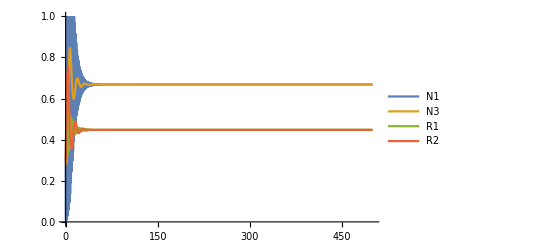

```mathematica
(* plot to make sure everything works as expected - the residents can coexist, no numerical problems, etc. *)
Plot[Evaluate[{N1[t],N3[t],R1[t], R2[t]}/.sol],{t,0, plotTMax},PlotLegends->{"N1","N3","R1","R2"}]
```

```mathematica
(* get the temporal mean of resource levels *)
RBar2 = Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.447619,0.447619}

```mathematica
RBarAll
```

{0.447581,0.448374}

```mathematica
(* examine mean resource fluctuations (away from the equilbirium levels *)
ConstantArray[RBar2,3]-RStar//MatrixForm
```

(0.0000381181 | -0.000762362
0.0000381181 | 0.123479
0.0000381181 | -1.9059×10^-6)

```mathematica
(* the mean of the square of resource levels, intermediate quantity in the calculation of resource variation *)
RSqBar2=Integrate[Evaluate[{R1Sq[t],R2Sq[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.200363,0.200363}

```mathematica
(* temporal variation in resource levels *)
RVar2=RSqBar2-RBar2^2
```

{0.,0.}

```mathematica
(* scaling factors *)
preQ = Phi[[2]].Inverse[Drop[Phi,{2}]];
q2 = Insert[-preQ,1,2]
(* the simple comparison *)
noQ2 = {-1/2,1,-1/2}
(* generation time scaling and beta scaling (the methods are equivalent in this model) *)
GTS2 = {-(1/2)(b2/b1),1,-(1/2)(b2/b3)}//N
```

{-0.000118894,1,-0.762212}

{-1/2,1,-1/2}

{-0.005,1.,-0.5}

{-0.0139028,1,-1.39028}

```mathematica
(* intermediate quantities needed for the computation of exact coexistence mechanisms *)
(* functions to give per-capita growth rates of the consumers *)
r1Func=Interpolation[Table[{t,dN1dt/N1[t]/.sol},{t,burnIn,tMax,0.1}]];
r2Func=Interpolation[Table[{t,dN2dt/N2[t]/.sol},{t,burnIn,tMax,0.1}]];
r3Func=Interpolation[Table[{t,dN3dt/N3[t]/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
r1F1FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R1[t]->RStar[[1,1]])/.sol},{t,burnIn,tMax,0.1}]];
r2F1FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R1[t]->RStar[[2,1]])/.sol},{t,burnIn,tMax,0.1}]];
r3F1FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R1[t]->RStar[[3,1]])/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
r1F2FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R2[t]->RStar[[1,2]])/.sol},{t,burnIn,tMax,0.1}]];
r2F2FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R2[t]->RStar[[2,2]])/.sol},{t,burnIn,tMax,0.1}]];
r3F2FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R2[t]->RStar[[3,2]])/.sol},{t,burnIn,tMax,0.1}]];

(* long-term average growth rates of the consumers *)
avgGR2=Integrate[{r1Func[t],r2Func[t],r3Func[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
avgGRF1Fixed2=Integrate[{r1F1FixedFunc[t],r2F1FixedFunc[t],r3F1FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
avgGRF2Fixed2=Integrate[{r1F2FixedFunc[t],r2F2FixedFunc[t],r3F2FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where both resources are fixed; no simulation data needed*)
avgGRF1F2Fixed2={dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]}/.{R1[t]->RBar2[[1]], R2[t]->RBar2[[2]]}
```

{-1.04083×10^-15,0.0804708,0.}

{-0.00381181,0.0804689,-1.9059×10^-6}

{0.00381181,1.9059×10^-6,1.9059×10^-6}

{-1.04083×10^-15,0.0804708,0.}

## Invasion analysis: species 3 is the invader

```mathematica
(* simulation parameters *)
N1Init=0.3;
N2Init=0.3;
N3Init =0;
R1Init =0.3;
R2Init=0.3;
burnIn=1000;
tMax=2000;
plotTMax = 500;
```

```mathematica
(* simulate to get data for coexistence mechanism calculations*)
sol=NDSolve[{N1'[t]==dN1dt,N2'[t]==dN2dt,R1'[t]==dR1dt,R2'[t]==dR2dt,R1Sq[t]==(R1[t])^2,R2Sq[t]==(R2[t])^2,N1[0]==N1Init,N2[0]==N2Init,R1[0]==R1Init,R2[0]==R2Init}/.N3[t]->0,{N1,N2,R1,R2,R1Sq,R2Sq},{t,0,tMax}][[1]];
```

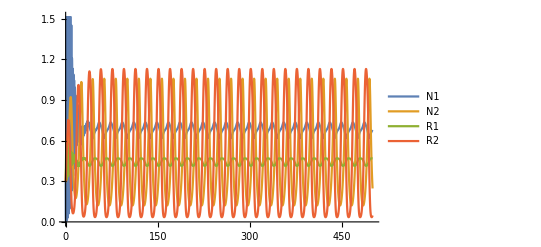

```mathematica
(* plot to make sure everything works as expected - the residents can coexist, no numerical problems, etc. *)
Plot[Evaluate[{N1[t],N2[t],R1[t], R2[t]}/.sol],{t,0, plotTMax},PlotLegends->{"N1","N2","R1","R2"}]
```

```mathematica
(* get the temporal mean of resource levels *)
RBar3 = Integrate[Evaluate[{R1[t],R2[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.444819,0.503631}

```mathematica
RBarAll
```

{0.447581,0.448374}

```mathematica
(* examine mean resource fluctuations (away from the equilbirium levels *)
ConstantArray[RBar3,3]-RStar//MatrixForm
```

(-0.00276243 | 0.0552498
-0.00276243 | 0.179491
-0.00276243 | 0.0560103)

```mathematica
(* the mean of the square of resource levels, intermediate quantity in the calculation of resource variation *)
RSqBar3=Integrate[Evaluate[{R1Sq[t],R2Sq[t]}/.sol],{t,burnIn,tMax}]/(tMax-burnIn)
```

{0.198293,0.422976}

```mathematica
(* temporal variation in resource levels *)
RVar3=RSqBar3-RBar3^2
```

{0.000429894,0.169331}

```mathematica
(* scaling factors *)
preQ = Phi[[3]].Inverse[Drop[Phi,{3}]];
q3= Insert[-preQ,1,3]//N
(* the simple comparison *)
noQ3 = {-1/2,-1/2,1}//N
(* generation time scaling and beta scaling (the methods are equivalent in this model) *)
GTS3 = {-(1/2)(b3/b1),-(1/2)(b3/b2),1}//N
```

{0.000155985,-1.31197,1.}

{-0.5,-0.5,1.}

{-0.005,-0.5,1.}

```mathematica
(* intermediate quantities needed for the computation of exact coexistence mechanisms *)
(* functions to give per-capita growth rates of the consumers *)
r1Func=Interpolation[Table[{t,dN1dt/N1[t]/.sol},{t,burnIn,tMax,0.1}]];
r2Func=Interpolation[Table[{t,dN2dt/N2[t]/.sol},{t,burnIn,tMax,0.1}]];
r3Func=Interpolation[Table[{t,dN3dt/N3[t]/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
r1F1FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R1[t]->RStar[[1,1]])/.sol},{t,burnIn,tMax,0.1}]];
r2F1FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R1[t]->RStar[[2,1]])/.sol},{t,burnIn,tMax,0.1}]];
r3F1FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R1[t]->RStar[[3,1]])/.sol},{t,burnIn,tMax,0.1}]];

(* functions to give per-capita growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
r1F2FixedFunc=Interpolation[Table[{t,(dN1dt/N1[t]/.R2[t]->RStar[[1,2]])/.sol},{t,burnIn,tMax,0.1}]];
r2F2FixedFunc=Interpolation[Table[{t,(dN2dt/N2[t]/.R2[t]->RStar[[2,2]])/.sol},{t,burnIn,tMax,0.1}]];
r3F2FixedFunc=Interpolation[Table[{t,(dN3dt/N3[t]/.R2[t]->RStar[[3,2]])/.sol},{t,burnIn,tMax,0.1}]];

(* long-term average growth rates of the consumers *)
avgGR3=Integrate[{r1Func[t],r2Func[t],r3Func[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F1 (resource 1) is fixed *)
avgGRF1Fixed3=Integrate[{r1F1FixedFunc[t],r2F1FixedFunc[t],r3F1FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where F2 (resource 2) is fixed *)
avgGRF2Fixed3=Integrate[{r1F2FixedFunc[t],r2F2FixedFunc[t],r3F2FixedFunc[t]},{t,burnIn,tMax}]/(tMax-burnIn)
(* long-term average growth rates of the consumers, in a hypothetical worlds where both resources are fixed; no simulation data needed*)
avgGRF1F2Fixed3={dN1dt/N1[t],dN2dt/N2[t],dN3dt/N3[t]}/.{R1[t]->RBar3[[1]], R2[t]->RBar3[[2]]}
```

{6.46027×10^-6,-0.000254175,0.0558721}

{0.276249,-0.000116054,0.0560103}

{-0.276243,-0.000138121,-0.000138121}

{6.46032×10^-6,0.109582,0.0558721}

## Tables of small-noise coexistence mechanisms

As discussed in the main text, the generation time scaling is equivalent to the β scaling in this model. Therefore,  we repeat the coexistence mechanisms values corresponding to the generation time scaling (row 4 in the table, not including headers).

```mathematica
spInd = 1;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN};
T1={{rPrime[q1, Phi,RStar], 0,"NA","NA" ,deltaN[q1, Psi, RVar1]},

{0, deltaRhoNew[noQ1, Phi, RBar1, RStar],deltaRhoF1New[noQ1, Phi, RBar1, RStar],deltaRhoF2New[noQ1, Phi, RBar1, RStar] ,deltaNNew[noQ1, Psi, RVar1]},

{0, deltaRhoNew[GTS1, Phi, RBar1, RStar],deltaRhoF1New[GTS1, Phi, RBar1, RStar],deltaRhoF2New[GTS1, Phi, RBar1, RStar] ,deltaNNew[GTS1, Psi, RVar1]},

{0, deltaRhoNew[GTS1, Phi, RBar1, RStar],deltaRhoF1New[GTS1, Phi, RBar1, RStar],deltaRhoF2New[GTS1, Phi, RBar1, RStar] ,deltaNNew[GTS1, Psi, RVar1]},

{0,deltaRhoNewII[Phi, RBar1, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar1, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar1, RBarHigh, spInd] ,deltaNNewII[Psi, RVar1, RVarHigh, spInd] }};
DecimalForm[MatrixForm[Prepend[T1,names]],{10,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN
-792.237 | 0 | NA | NA | 1085.443
0 | 100.976 | 101.237 | -0.261 | 0.065
0 | 95.742 | 96.223 | -0.481 | 6.453
0 | 95.742 | 96.223 | -0.481 | 6.453
0 | 101.029 | 101.288 | -0.259 | 0.000)

```mathematica
spInd = 2;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN};
T2={{rPrime[q2, Phi,RStar], 0,"NA","NA" ,deltaN[q2, Psi, RVar2]},

{0, deltaRhoNew[noQ2, Phi, RBar2, RStar],deltaRhoF1New[noQ2, Phi, RBar2, RStar],deltaRhoF2New[noQ2, Phi, RBar2, RStar] ,deltaNNew[noQ2, Psi, RVar2]},

{0, deltaRhoNew[GTS2, Phi, RBar2, RStar],deltaRhoF1New[GTS2, Phi, RBar2, RStar],deltaRhoF2New[GTS2, Phi, RBar2, RStar] ,deltaNNew[GTS2, Psi, RVar2]},

{0, deltaRhoNew[GTS2, Phi, RBar2, RStar],deltaRhoF1New[GTS2, Phi, RBar2, RStar],deltaRhoF2New[GTS2, Phi, RBar2, RStar] ,deltaNNew[GTS2, Psi, RVar2]},

{0,deltaRhoNewII[Phi, RBar2, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar2, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar2, RBarHigh, spInd] ,deltaNNewII[Psi, RVar2, RVarHigh, spInd] }};
DecimalForm[MatrixForm[Prepend[T2,names]],{10,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN
0.094 | 0 | NA | NA | 0.000
0 | 0.094 | -0.002 | 0.096 | 0.000
0 | 0.094 | -0.000 | 0.094 | 0.000
0 | 0.094 | -0.000 | 0.094 | 0.000
0 | -0.001 | 0.000 | -0.001 | 0.117)

```mathematica
spInd = 3;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN};
T3={{rPrime[q3, Phi,RStar], 0,"NA","NA" ,deltaN[q3, Psi, RVar3]},

{0, deltaRhoNew[noQ3, Phi, RBar3, RStar],deltaRhoF1New[noQ3, Phi, RBar3, RStar],deltaRhoF2New[noQ3, Phi, RBar3, RStar] ,deltaNNew[noQ3, Psi, RVar3]},

{0, deltaRhoNew[GTS3, Phi, RBar3, RStar],deltaRhoF1New[GTS3, Phi, RBar3, RStar],deltaRhoF2New[GTS3, Phi, RBar3, RStar] ,deltaNNew[GTS3, Psi, RVar3]},

{0, deltaRhoNew[GTS3, Phi, RBar3, RStar],deltaRhoF1New[GTS3, Phi, RBar3, RStar],deltaRhoF2New[GTS3, Phi, RBar3, RStar] ,deltaNNew[GTS3, Psi, RVar3]},

{0,deltaRhoNewII[Phi, RBar3, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar3, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar3, RBarHigh, spInd] ,deltaNNewII[Psi, RVar3, RVarHigh, spInd] }};
DecimalForm[MatrixForm[Prepend[T3,names]],{10,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN
-0.124 | 0 | NA | NA | 0.234
0 | -0.013 | 0.138 | -0.151 | 0.089
0 | -0.013 | 0.001 | -0.014 | 0.089
0 | -0.013 | 0.001 | -0.014 | 0.089
0 | 0.055 | -0.000 | 0.055 | 0.000)

### Tables in Latex format

```mathematica
method={"Scaling factors","Simple comparison","Generation time scaling","β scaling","Invader-invader comparison"};
```

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["1",5]},{method},Transpose[T1]]],{6,3}]//TeXForm
```

\left(
\begin{array}{ccccccc}
 1 & \text{Scaling factors} & -792.237 & 0 & \text{NA} & \text{NA} & 1085.440 \\
 1 & \text{Simple comparison} & 0 & 100.976 & 101.237 & -0.261 & 0.065 \\
 1 & \text{Generation time scaling} & 0 & 95.742 & 96.223 & -0.481 & 6.453 \\
 1 & \text{$\beta $ scaling} & 0 & 95.742 & 96.223 & -0.481 & 6.453 \\
 1 & \text{Invader-invader comparison} & 0 & 101.029 & 101.288 & -0.259 & 0.000 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["2",5]},{method},Transpose[T2]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccccc}
 2 & \text{Scaling factors} & 0.094 & 0 & \text{NA} & \text{NA} & 0.000 \\
 2 & \text{Simple comparison} & 0 & 0.094 & -0.002 & 0.096 & 0.000 \\
 2 & \text{Generation time scaling} & 0 & 0.094 & -0.000 & 0.094 & 0.000 \\
 2 & \text{$\beta $ scaling} & 0 & 0.094 & -0.000 & 0.094 & 0.000 \\
 2 & \text{Invader-invader comparison} & 0 & -0.001 & 0.000 & -0.001 & 0.117 \\
\end{array}
\right)

```mathematica
DecimalForm[Transpose[Join[{ConstantArray["3",5]},{method},Transpose[T3]]],{10,3}]//TeXForm
```

\left(
\begin{array}{ccccccc}
 3 & \text{Scaling factors} & -0.124 & 0 & \text{NA} & \text{NA} & 0.234 \\
 3 & \text{Simple comparison} & 0 & -0.013 & 0.138 & -0.151 & 0.089 \\
 3 & \text{Generation time scaling} & 0 & -0.013 & 0.001 & -0.014 & 0.089 \\
 3 & \text{$\beta $ scaling} & 0 & -0.013 & 0.001 & -0.014 & 0.089 \\
 3 & \text{Invader-invader comparison} & 0 & 0.055 & -0.000 & 0.055 & 0.000 \\
\end{array}
\right)

## Tables of small-noise coexistence mechanisms, exact coexistence mechanisms, the approximate invasion growth rate (i.e., the sum of small-noise mechanisms), and the exact invasion growth rate)

```mathematica
spInd = 1;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN,rPrime^(e),Δρ^(e),ΔρF1^(e),ΔρF2^(e),ΔN^(e),invGR, invGR^(e)};
T1={{rPrime[q1, Phi,RStar], 0,"NA","NA" ,deltaN[q1, Psi, RVar1],
 rPrimeE[q1,  avgGRF1F2Fixed1],0,"NA","NA",deltaNE[q1,avgGRF1F2Fixed1,avgGR1],
rPrime[q1, Phi,RStar]+deltaN[q1, Psi, RVar1],avgGR1[[spInd]] },

{0, deltaRhoNew[noQ1, Phi, RBar1, RStar],deltaRhoF1New[noQ1, Phi, RBar1, RStar],deltaRhoF2New[noQ1, Phi, RBar1, RStar] ,deltaNNew[noQ1, Psi, RVar1], 
0,deltaRhoENew[noQ1 , avgGRF1F2Fixed1],deltaRhoF1ENew[noQ1 , avgGRF2Fixed1],deltaRhoF2ENew[noQ1 , avgGRF1Fixed1],deltaNENew[noQ1 , avgGRF1F2Fixed1,avgGR1],
deltaRhoNew[noQ1, Phi, RBar1, RStar]+deltaNNew[noQ1, Psi, RVar1],avgGR1[[spInd]]},

{0, deltaRhoNew[GTS1, Phi, RBar1, RStar],deltaRhoF1New[GTS1, Phi, RBar1, RStar],deltaRhoF2New[GTS1, Phi, RBar1, RStar] ,deltaNNew[GTS1, Psi, RVar1],
0,deltaRhoENew[GTS1 , avgGRF1F2Fixed1],deltaRhoF1ENew[GTS1 , avgGRF2Fixed1],deltaRhoF2ENew[GTS1 , avgGRF1Fixed1],deltaNENew[GTS1 , avgGRF1F2Fixed1,avgGR1],
 deltaRhoNew[GTS1 , Phi, RBar1, RStar]+deltaNNew[GTS1 , Psi, RVar1],avgGR1[[spInd]]},

{0, deltaRhoNew[GTS1, Phi, RBar1, RStar],deltaRhoF1New[GTS1, Phi, RBar1, RStar],deltaRhoF2New[GTS1, Phi, RBar1, RStar] ,deltaNNew[GTS1, Psi, RVar1],
0,deltaRhoENew[GTS1 , avgGRF1F2Fixed1],deltaRhoF1ENew[GTS1 , avgGRF2Fixed1],deltaRhoF2ENew[GTS1 , avgGRF1Fixed1],deltaNENew[GTS1 , avgGRF1F2Fixed1,avgGR1],
 deltaRhoNew[GTS1 , Phi, RBar1, RStar]+deltaNNew[GTS1 , Psi, RVar1],avgGR1[[spInd]]},

{0,deltaRhoNewII[Phi, RBar1, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar1, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar1, RBarHigh, spInd] ,deltaNNewII[Psi, RVar1, RVarHigh, spInd] ,
0,deltaRhoENewII[avgGRF1F2Fixed1,avgGRF1F2FixedHigh, spInd],deltaRhoF1ENewII[avgGRF2Fixed1,avgGRF2FixedHigh, spInd],deltaRhoF2ENewII[avgGRF1Fixed1, avgGRF1FixedHigh, spInd],deltaNENewII[ avgGRF1F2Fixed1,avgGR1, avgGRF1F2FixedHigh,avgGRHigh, spInd],
deltaRhoNewII[Phi, RBar1, RBarHigh, spInd] + deltaNNewII[Psi, RVar1, RVarHigh, spInd],avgGR1[[spInd]]}};
DecimalForm[MatrixForm[Prepend[T1,names]],{10,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN | rPrime^e | Δρ^e | ΔρF1^e | ΔρF2^e | ΔN^e | invGR | invGR^e
-7.923 | 0 | NA | NA | 10.855 | -7.498 | 0 | NA | NA | 8.520 | 2.932 | 1.010
0 | 0.957 | 0.962 | -0.005 | 0.065 | 0 | 0.960 | 0.962 | 0.048 | 0.051 | 1.022 | 1.010
0 | 0.957 | 0.962 | -0.005 | 0.065 | 0 | 0.960 | 0.962 | 0.048 | 0.051 | 1.022 | 1.010
0 | 0.991 | 0.978 | 0.013 | 0.023 | 0 | 0.992 | 0.978 | 0.032 | 0.018 | 1.015 | 1.010
0 | 1.010 | 1.013 | -0.002 | 0.000 | 0 | 1.010 | 1.013 | -0.002 | -0.000 | 1.010 | 1.010)

```mathematica
spInd = 2;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN,rPrime^(e),Δρ^(e),ΔρF1^(e),ΔρF2^(e),ΔN^(e),invGR, invGR^(e)};
T2={{rPrime[q2, Phi,RStar], 0,"NA","NA",deltaN[q2, Psi, RVar2],
 rPrimeE[q2,  avgGRF1F2Fixed2],0,"NA","NA",deltaNE[q2,avgGRF1F2Fixed2,avgGR2],
rPrime[q2, Phi,RStar]+deltaN[q2, Psi, RVar2],avgGR2[[spInd]] },

{0, deltaRhoNew[noQ2, Phi, RBar2, RStar],deltaRhoF1New[noQ2, Phi, RBar2, RStar],deltaRhoF2New[noQ2, Phi, RBar2, RStar] ,deltaNNew[noQ2, Psi, RVar2], 
0,deltaRhoENew[noQ2 , avgGRF1F2Fixed2],deltaRhoF1ENew[noQ2 , avgGRF2Fixed2],deltaRhoF2ENew[noQ2 , avgGRF1Fixed2],deltaNENew[noQ2 , avgGRF1F2Fixed2,avgGR2],
deltaRhoNew[noQ2, Phi, RBar2, RStar]+deltaNNew[noQ2, Psi, RVar2],avgGR2[[spInd]]},

{0, deltaRhoNew[GTS2, Phi, RBar2, RStar],deltaRhoF1New[GTS2, Phi, RBar2, RStar],deltaRhoF2New[GTS2, Phi, RBar2, RStar] ,deltaNNew[GTS2, Psi, RVar2],
0,deltaRhoENew[GTS2 , avgGRF1F2Fixed2],deltaRhoF1ENew[GTS2 , avgGRF2Fixed2],deltaRhoF2ENew[GTS2 , avgGRF1Fixed2],deltaNENew[GTS2 , avgGRF1F2Fixed2,avgGR2],
 deltaRhoNew[GTS2 , Phi, RBar2, RStar]+deltaNNew[GTS2 , Psi, RVar2],avgGR2[[spInd]]},

{0, deltaRhoNew[GTS2, Phi, RBar2, RStar],deltaRhoF1New[GTS2, Phi, RBar2, RStar],deltaRhoF2New[GTS2, Phi, RBar2, RStar] ,deltaNNew[GTS2, Psi, RVar2],
0,deltaRhoENew[GTS2 , avgGRF1F2Fixed2],deltaRhoF1ENew[GTS2 , avgGRF2Fixed2],deltaRhoF2ENew[GTS2 , avgGRF1Fixed2],deltaNENew[GTS2 , avgGRF1F2Fixed2,avgGR2],
 deltaRhoNew[GTS2 , Phi, RBar2, RStar]+deltaNNew[GTS2 , Psi, RVar2],avgGR2[[spInd]]},

{0,deltaRhoNewII[Phi, RBar2, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar2, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar2, RBarHigh, spInd] ,deltaNNewII[Psi, RVar2, RVarHigh, spInd] ,
0,deltaRhoENewII[avgGRF1F2Fixed2,avgGRF1F2FixedHigh, spInd],deltaRhoF1ENewII[avgGRF2Fixed2,avgGRF2FixedHigh, spInd],deltaRhoF2ENewII[avgGRF1Fixed2, avgGRF1FixedHigh, spInd],deltaNENewII[ avgGRF1F2Fixed2,avgGR2, avgGRF1F2FixedHigh,avgGRHigh, spInd],
deltaRhoNewII[Phi, RBar2, RBarHigh, spInd] + deltaNNewII[Psi, RVar2, RVarHigh, spInd],avgGR2[[spInd]]}};
NumberForm[MatrixForm[Prepend[T2,names]],{3,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN | rPrime^e | Δρ^e | ΔρF1^e | ΔρF2^e | ΔN^e | invGR | invGR^e
0.094 | 0 | NA | NA | 0.000 | 0.080 | 0 | NA | NA | 6.690×10^-15 | 0.094 | 0.080
0 | 0.094 | 6.140×10^-7 | 0.094 | 0.000 | 0 | 0.080 | 6.140×10^-7 | 0.080 | 6.700×10^-15 | 0.094 | 0.080
0 | 0.094 | 6.140×10^-7 | 0.094 | 0.000 | 0 | 0.080 | 6.140×10^-7 | 0.080 | 6.700×10^-15 | 0.094 | 0.080
0 | 0.094 | 1.820×10^-6 | 0.094 | 0.000 | 0 | 0.080 | 1.820×10^-6 | 0.080 | 6.710×10^-15 | 0.094 | 0.080
0 | 0.001 | -0.000 | 0.001 | 0.117 | 0 | 0.001 | -0.000 | 0.082 | 0.081 | 0.118 | 0.080)

```mathematica
spInd = 3;
names = {rPrime,Δρ,ΔρF1,ΔρF2,ΔN,rPrime^(e),Δρ^(e),ΔρF1^(e),ΔρF2^(e),ΔN^(e),invGR, invGR^(e)};
T3={{rPrime[q3, Phi,RStar], 0,"NA","NA" ,deltaN[q3, Psi, RVar3],
 rPrimeE[q3,  avgGRF1F2Fixed3],0,"NA","NA",deltaNE[q3,avgGRF1F2Fixed3,avgGR3],
rPrime[q3, Phi,RStar]+deltaN[q3, Psi, RVar3],avgGR3[[spInd]] },

{0, deltaRhoNew[noQ3, Phi, RBar3, RStar],deltaRhoF1New[noQ3, Phi, RBar3, RStar],deltaRhoF2New[noQ3, Phi, RBar3, RStar] ,deltaNNew[noQ3, Psi, RVar3], 
0,deltaRhoENew[noQ3, avgGRF1F2Fixed3],deltaRhoF1ENew[noQ3, avgGRF2Fixed3],deltaRhoF2ENew[noQ3, avgGRF1Fixed3],deltaNENew[noQ3, avgGRF1F2Fixed3,avgGR3],
deltaRhoNew[noQ3, Phi, RBar3, RStar]+deltaNNew[noQ3, Psi, RVar3],avgGR3[[spInd]]},

{0, deltaRhoNew[GTS3, Phi, RBar3, RStar],deltaRhoF1New[GTS3, Phi, RBar3, RStar],deltaRhoF2New[GTS3, Phi, RBar3, RStar] ,deltaNNew[GTS3, Psi, RVar3],
0,deltaRhoENew[GTS3, avgGRF1F2Fixed3],deltaRhoF1ENew[GTS3, avgGRF2Fixed3],deltaRhoF2ENew[GTS3, avgGRF1Fixed3],deltaNENew[GTS3, avgGRF1F2Fixed3,avgGR3],
 deltaRhoNew[GTS3, Phi, RBar3, RStar]+deltaNNew[GTS3, Psi, RVar3],avgGR3[[spInd]]},

{0, deltaRhoNew[GTS3, Phi, RBar3, RStar],deltaRhoF1New[GTS3, Phi, RBar3, RStar],deltaRhoF2New[GTS3, Phi, RBar3, RStar] ,deltaNNew[GTS3, Psi, RVar3],
0,deltaRhoENew[GTS3, avgGRF1F2Fixed3],deltaRhoF1ENew[GTS3, avgGRF2Fixed3],deltaRhoF2ENew[GTS3, avgGRF1Fixed3],deltaNENew[GTS3, avgGRF1F2Fixed3,avgGR3],
 deltaRhoNew[GTS3, Phi, RBar3, RStar]+deltaNNew[GTS3, Psi, RVar3],avgGR3[[spInd]]},

{0,deltaRhoNewII[Phi, RBar3, RBarHigh, spInd],deltaRhoF1NewII[ Phi, RBar3, RBarHigh, spInd],deltaRhoF2NewII[ Phi, RBar3, RBarHigh, spInd] ,deltaNNewII[Psi, RVar3, RVarHigh, spInd] ,
0,deltaRhoENewII[avgGRF1F2Fixed3,avgGRF1F2FixedHigh, spInd],deltaRhoF1ENewII[avgGRF2Fixed3,avgGRF2FixedHigh, spInd],deltaRhoF2ENewII[avgGRF1Fixed3, avgGRF1FixedHigh, spInd],deltaNENewII[ avgGRF1F2Fixed3,avgGR3, avgGRF1F2FixedHigh,avgGRHigh, spInd],
deltaRhoNewII[Phi, RBar3, RBarHigh, spInd] + deltaNNewII[Psi, RVar3, RVarHigh, spInd],avgGR3[[spInd]]}};
DecimalForm[MatrixForm[Prepend[T3,names]],{3,3}]
```

(rPrime | Δρ | ΔρF1 | ΔρF2 | ΔN | rPrime^e | Δρ^e | ΔρF1^e | ΔρF2^e | ΔN^e | invGR | invGR^e
-0.124 | 0 | NA | NA | 0.228 | -0.088 | 0 | NA | NA | 0.141 | 0.104 | 0.054
0 | -0.013 | 0.001 | -0.015 | 0.087 | 0 | -0.000 | 0.001 | 0.052 | 0.054 | 0.073 | 0.054
0 | -0.013 | 0.001 | -0.015 | 0.087 | 0 | -0.000 | 0.001 | 0.052 | 0.054 | 0.073 | 0.054
0 | -0.013 | 0.000 | -0.013 | 0.087 | 0 | -0.000 | -0.000 | 0.054 | 0.054 | 0.073 | 0.054
0 | 0.056 | -0.000 | 0.056 | 0.000 | 0 | 0.056 | -0.000 | 0.056 | -0.000 | 0.056 | 0.054)